#### Коллапс данных квадрата намагниченности

Возьмём набор данных из симуляций Двумерного Изинга при нулевом внешнем поле

Пусть мы будем рассматривать длины 10-100 с шагом 10, а абсолютную температуру - 1/J, где J - 0.1-0.6, 0.7-0.9 с шагом 0.01

```mathematica
allData={};
```

```mathematica
Do[
ColWithT={10/J};
data=Import[StringJoin["https://raw.githubusercontent.com/kamilla0503/saw/master/Ising/BC/M_counts_and_contacts_0.",ToString[J],"00000_0_higher_hpc.txt"],"Table"];
Col={};
Do[Col=Append[Col,data[[2+L]][[10]]],{L,{10,20,30,40,50,60,70,80,90,100}}];
ColWithT=Append[ColWithT,Col];
allData=Append[allData,ColWithT],{J,{1,2,3,4,5,6}}]
```

```mathematica
Do[
ColWithT={100/J};
data=Import[StringJoin["https://raw.githubusercontent.com/kamilla0503/saw/master/Ising/Calcs_3/M_counts_and_contacts_0.",ToString[J],"0000_0_higher_hpc.txt"],"Table"];
Col={};
Do[Col=Append[Col,data[[2+L]][[10]]],{L,{10,20,30,40,50,60,70,80,90,100}}];
ColWithT=Append[ColWithT,Col];
allData=Append[allData,ColWithT],{J,70,81}]
```

```mathematica
Do[
ColWithT={100/J};
data=Import[StringJoin["https://raw.githubusercontent.com/kamilla0503/saw/master/Ising/Calcs_3/M_counts_and_contacts_0.",ToString[J],"0000_0_higher_hpc.txt"],"Table"];
Col={};
Do[Col=Append[Col,data[[2+L]][[10]]],{L,{10,20,30,40,50,60,70,80,90,100}}];
ColWithT=Append[ColWithT,Col];
allData=Append[allData,ColWithT],{J,83,90}]
```

Рассмотрим пока немасштабированный график:

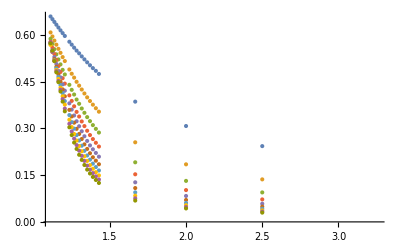

```mathematica
ListPlot[Table[Table[{allData[[i]][[1]],allData[[i]][[2]][[j]]},{i,Length[allData]}],{j,10}]]
```

Возникают заметные и растущие расхождения

Перейдём к масштабированию графика: заменим T на (T-Tc), а значение квадрата умножим на L^(-γ/v)

```mathematica
Tc=1/0.835
```

1.1976

```mathematica
Ls={10,20,30,40,50,60,70,80,90,100};
```

```mathematica
Manipulate[ListPlot[Table[Table[{(allData[[i]][[1]] - Tc)*Ls[[j]]^(1/2v),allData[[i]][[2]][[j]]*Ls[[j]]^(b/v)},{i,Length[allData]}],{j,10}],Joined->True],{v,1,5,0.1},{γ,1,5,0.1}]
```

Part::partw: Part 3 of {0.73,0.156066} does not exist.

Part::partw: Part 3 of {0.73,0.11404} does not exist.

Part::partw: Part 3 of {0.73,0.0737083} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of {100,0.73,0.156066} does not exist.

Part::partw: Part 4 of {150,0.73,0.11404} does not exist.

Part::partw: Part 4 of {250,0.73,0.0737083} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of {300,0.73,0.0625612} does not exist.

Part::partw: Part 4 of {350,0.73,0.054289} does not exist.

Part::partw: Part 4 of {500,0.73,0.038933} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 7 of {300,350,500,600,750,1000} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 7 of {300,350,500,600,750,1000} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 7 of {300,350,500,600,750,1000} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 7 of {300,350,500,600,750,1000} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 7 of {300,350,500,600,750,1000} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 7 of {300,350,500,600,750,1000} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 5 of {250,0.73,1.03736,1.08545} does not exist.

Part::partw: Part 5 of {300,0.73,1.03986,1.08919} does not exist.

Part::partw: Part 5 of {350,0.73,1.04164,1.09182} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Пересечение почти достигнуто при увеличении v, но этого недостаточно: стоит попробовать покрутить и Tc:

```mathematica
Manipulate[ListPlot[Table[Table[{(allData[[i]][[1]] - Tc)*Ls[[j]]^(1/v),allData[[i]][[2]][[j]]*Ls[[j]]^(b/v)},{i,Length[allData]}],{j,1,10,1}], PlotRange->{{-3,3}, All}, Joined->True],{v,0.9,1.1,0.02},{b,0.1,0.2,0.01},{Tc,1/0.835-0.2,1/0.835+0.2,0.01}]
```

Part::partw: Part 4 of {300,0.73,0.0625612} does not exist.

Part::partw: Part 4 of {350,0.73,0.054289} does not exist.

Part::partw: Part 4 of {500,0.73,0.038933} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of {300,0.73,0.0625612} does not exist.

Part::partw: Part 4 of {350,0.73,0.054289} does not exist.

Part::partw: Part 4 of {500,0.73,0.038933} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 5 of {250,0.73,1.03736,1.08545} does not exist.

Part::partw: Part 5 of {300,0.73,1.03986,1.08919} does not exist.

Part::partw: Part 5 of {350,0.73,1.04164,1.09182} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of {300,0.73,0.0625612} does not exist.

Part::partw: Part 4 of {350,0.73,0.054289} does not exist.

Part::partw: Part 4 of {500,0.73,0.038933} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 5 of {250,0.73,1.03736,1.08545} does not exist.

Part::partw: Part 5 of {300,0.73,1.03986,1.08919} does not exist.

Part::partw: Part 5 of {350,0.73,1.04164,1.09182} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of {500,0.73,0.038933} does not exist.

Part::partw: Part 4 of {600,0.73,0.0327412} does not exist.

Part::partw: Part 4 of {750,0.73,0.0264081} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

28.02.2021 (Коллапс данных квадрата намагниченности при больших длинах (N > 100))

```mathematica
newData=Import["https://raw.githubusercontent.com/kamilla0503/saw/master/Ising/Canonical_near_phase/all.txt", "Table"];
```

Возьмём длины 100-1000

```mathematica
allData={};
Ls={600,750,1000}
Do[
AppendTo[allData,Select[newData,#[[1]]==L&][[All,{1,2,16}]]];
,{L,Ls}]
```

{600,750,1000}

Стоит отметить, что в формулах фигурируют не длины систем, а их квадратные корни (так как N = L * L, где L - используемая в формулах величина)

```mathematica
Manipulate[ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v),#[[3]]*(#[[1]])^(b/v)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-10,10}, All}, Joined->JoinQ, Mesh->DotsQ, AxesLabel->{"t L^(1/v)", "m^2 L^(2  b/v)"}],{v,0.95,1.5,0.01},{b,0.11,0.2,0.002},{Tc,1/0.835-0.01,1/0.835+0.01,0.001}, {JoinQ,{True,False}},{DotsQ,{False,All}}]
```

MapAt::partw: Part {All,All} of allData does not exist.

General::stop: Further output of MapAt::partw will be suppressed during this calculation.

Part::partw: Part 2 of #1 does not exist.

ListPlot::lpn: MapAt[{(1./Part[«2»]-1. FE`Tc$$24) (#1⟦1⟧)^0.75,#1⟦3⟧ (#1⟦1⟧)^0.133333}&,allData,{All,All}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

MapAt::partw: Part {All,All} of allData does not exist.

General::stop: Further output of MapAt::partw will be suppressed during this calculation.

ListPlot::lpn: MapAt[{(1./Part[«2»]-1. FE`Tc$$28) (#1⟦1⟧)^0.75,#1⟦3⟧ (#1⟦1⟧)^0.133333}&,allData,{All,All}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

MapAt::partw: Part {All,All} of allData does not exist.

General::stop: Further output of MapAt::partw will be suppressed during this calculation.

ListPlot::lpn: MapAt[{(1./Part[«2»]-1. FE`Tc$$31) (#1⟦1⟧)^0.75,#1⟦3⟧ (#1⟦1⟧)^0.133333}&,allData,{All,All}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

MapAt::partw: Part {All,All} of allData does not exist.

General::stop: Further output of MapAt::partw will be suppressed during this calculation.

ListPlot::lpn: MapAt[{(1./Part[«2»]-1. FE`Tc$$35) (#1⟦1⟧)^0.75,#1⟦3⟧ (#1⟦1⟧)^0.133333}&,allData,{All,All}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

На данный момент лучший результат показывает v=1.01, b=0.12, а Tc=1,1976
(при увеличении Tc графики расходятся в прямом порядке легенды (чем выше график, тем меньше длина), при уменьшении же - в обратном (наибольшие длины поднимаются вверх))
(при увеличение b графики слева расходятся, а справа - сливаются, и наоборот; 0.12 - наиболее оптимальный вариант)

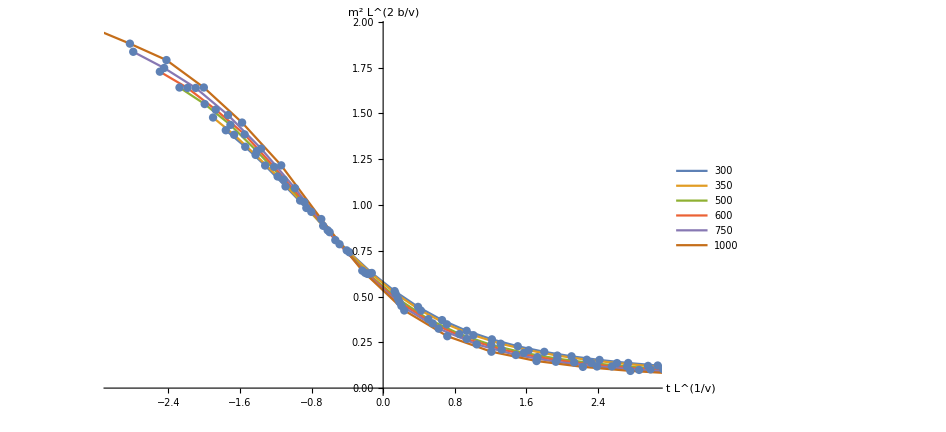

```mathematica
ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v),#[[3]]*(#[[1]])^(b/v)}&,allData,{All,All}]/.{v->1.01,b->0.12,Tc->1.1976},PlotLegends->Ls,PlotRange->{{-3,3}, All}, Joined->True, Mesh->All, AxesLabel->{"t L^(1/v)", "m^2 L^(2  b/v)"}, ImageSize->700]
```

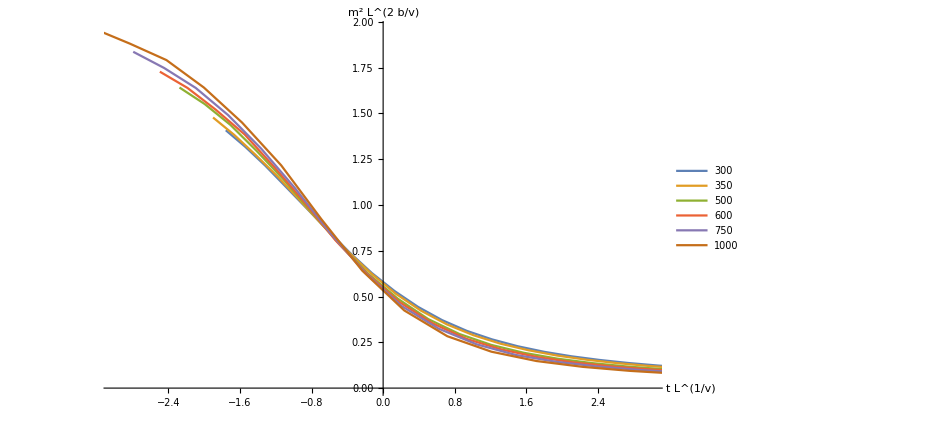

```mathematica
ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v),#[[3]]*(#[[1]])^(b/v)}&,allData,{All,All}]/.{v->1.01,b->0.12,Tc->1.1976},PlotLegends->Ls,PlotRange->{{-3,3}, All}, Joined->True, AxesLabel->{"t L^(1/v)", "m^2 L^(2  b/v)"}, ImageSize->700]
```

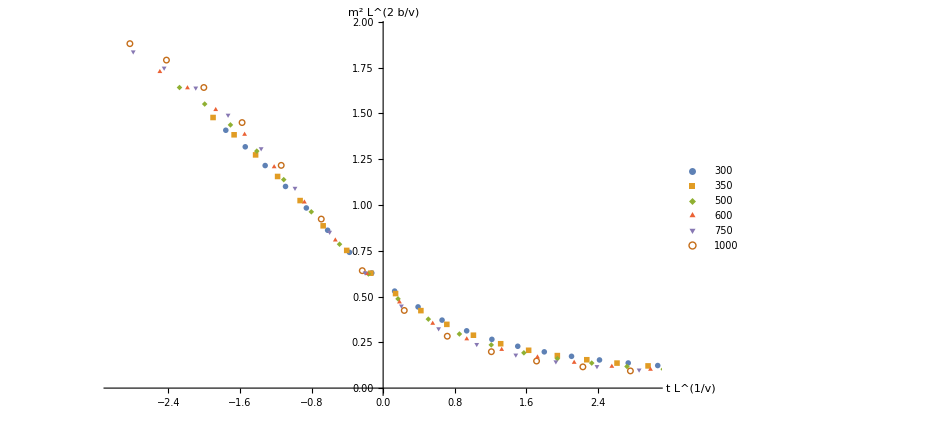

```mathematica
ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v),#[[3]]*(#[[1]])^(b/v)}&,allData,{All,All}]/.{v->1.01,b->0.12,Tc->1.1976},PlotLegends->Ls,PlotRange->{{-3,3}, All}, PlotMarkers->{Automatic,Medium}, AxesLabel->{"t L^(1/v)", "m^2 L^(2  b/v)"}, ImageSize->700]
```

28.02 .2021 (Коллапс данных теплоёмкости при больших длинах (N > 100))

```mathematica
newData=Import["https://raw.githubusercontent.com/kamilla0503/saw/master/Ising/Canonical_near_phase/all.txt", "Table"];
```

Возьмём длины 100-1000

```mathematica
allData={};
Ls={250,300,350,500,600,750,1000}
Do[
AppendTo[allData,Select[newData,#[[1]]==L&][[All,{1,2,8,10}]]];
,{L,Ls}]
```

{250,300,350,500,600,750,1000}

1-длина, 2-J, 8-энергия, 10-квадрат энергии

```mathematica
Manipulate[ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v),(#[[4]]-(#[[3]])^2)*(#[[2]])^2*#[[1]]*(#[[1]])^(-α/2v)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, Joined->JoinQ, Mesh->DotsQ,  AxesLabel->{"t L^(1/v)", "(⟨e^2⟩ - ⟨e⟩^2)*J^2*N(=L*L)*L^(α/v)"}],{v,0.95,1.05,0.01},{α,-0.1,0.1,0.01},{Tc,1/0.86,1/0.83,0.005}, {JoinQ,{True,False}},{DotsQ,{False,All}}]
```

Tc=1.1976
α=0.67
v=1.01

```mathematica
Manipulate[ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v),(#[[4]]-(#[[3]])^2)*(#[[2]])^2*#[[1]]*(#[[1]])^(-α/2v)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, Joined->JoinQ, Mesh->DotsQ,  AxesLabel->{"t L^(1/v)", "(⟨e^2⟩ - ⟨e⟩^2)*J^2*N(=L*L)*L^(α/v)"}],{v,0.95,1.05,0.01},{α,0,1,0.1},{Tc,1/0.86,1/0.83,0.005}, {JoinQ,{True,False}},{DotsQ,{False,All}}]
```

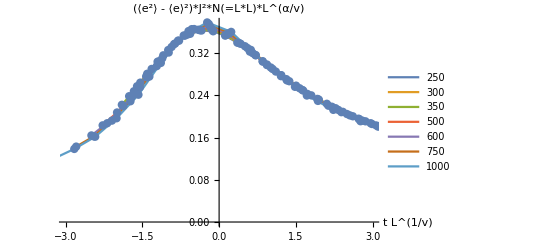

```mathematica
ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v),(#[[4]]-(#[[3]])^2)*(#[[2]])^2*#[[1]]*(#[[1]])^(-α/2v)}&,allData,{All,All}]/.{Tc->1.1976,α->0.67,v->1.01},PlotLegends->Ls,PlotRange->{{-3,3}, All}, Joined->True, Mesh->All, AxesLabel->{"t L^(1/v)", "(⟨e^2⟩ - ⟨e⟩^2)*J^2*N(=L*L)*L^(α/v)"}]
```